```mathematica
Msun=1.98855 10^33;
```

```mathematica
MassData=Import[ParentDirectory[NotebookDirectory[]]<>"/mass.dat","Table","HeaderLines" -> 3];
```

```mathematica
MassSum=Table[∑_(j=2)^i MassData[[1,j]],{i,2,Length[MassData[[1,All]]]}];
```

Get::noopen: Cannot open CloudObjectLoader`.

```mathematica
table=Import[NotebookDirectory[]<>"WD-profile-M1.08-N108.dat","Table","HeaderLines" -> 1];
```

```mathematica
Export[NotebookDirectory[]<>"WD-profile-M1.08-N108.dat",Table[{j*0.01,table[[j,1]],table[[j,2]]},{j,1,108}]]
```

/Users/elvissoares/Dropbox/Doutorado/Delayed Thermalization/code/output/accretion/WD-profile-M1.08-N108.dat

```mathematica
ListPlot[EnergyData[[All,5]], Joined->True,PlotRange->All,PlotLegends->All]
```

-Graphics-

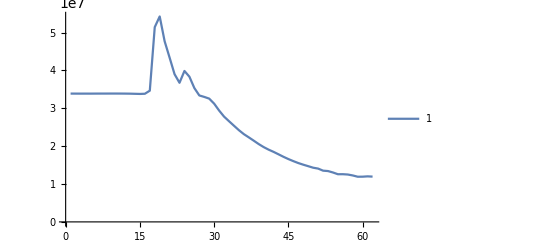

```mathematica
ListPlot[TemperatureData[[All,2]], Joined->True,PlotRange->{All,All},PlotLegends->All]
```

```mathematica
Time={1,2,5,10};
```

```mathematica
TemperatureData=Import[ParentDirectory[NotebookDirectory[]]<>"/temperature.dat","Table","HeaderLines" -> 3];
```

```mathematica
TemperatureMassData=Table[{MassSum[[i]]/Msun,TemperatureData[[Time[[1]],i+1]],TemperatureData[[Time[[2]],i+1]],TemperatureData[[Time[[3]],i+1]],TemperatureData[[Time[[4]],i+1]]},{i,1,Length[MassSum]}];
```

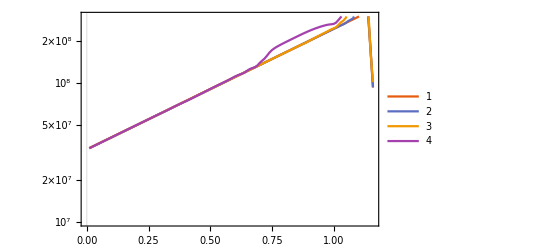

```mathematica
ListLogPlot[{TemperatureMassData[[All,{1,2}]],TemperatureMassData[[All,{1,3}]],TemperatureMassData[[All,{1,4}]],TemperatureMassData[[All,{1,5}]]}, Joined->True,PlotRange->{All,{10^7,3 10^8}},PlotLegends->All, PlotTheme-> "Scientific"]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/lagrangean/temperature.dat",TemperatureMassData,ExportForm->CForm];
```

## Pressure

```mathematica
PressureData=Import[ParentDirectory[NotebookDirectory[]]<>"/pressure.dat","Table","HeaderLines" -> 3];
```

```mathematica
PressureMassData=Table[{MassSum[[i]]/Msun,PressureData[[Time[[1]],i+1]],PressureData[[Time[[2]],i+1]],PressureData[[Time[[3]],i+1]],PressureData[[Time[[4]],i+1]]},{i,1,Length[MassSum]}];
```

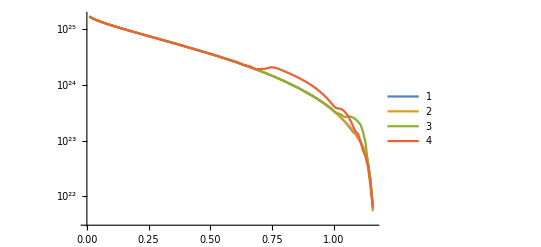

```mathematica
ListLogPlot[{PressureMassData[[All,{1,2}]],PressureMassData[[All,{1,3}]],PressureMassData[[All,{1,4}]],PressureMassData[[All,{1,5}]]}, Joined->True,PlotRange->All,PlotLegends->All]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/lagrangean/pressure.dat",PressureMassData,ExportForm->CForm];
```

## Nuclear Abundance

```mathematica
HeliumData=Import[ParentDirectory[NotebookDirectory[]]<>"/helium.dat","Table","HeaderLines" -> 3];
CarbonData=Import[ParentDirectory[NotebookDirectory[]]<>"/carbon.dat","Table","HeaderLines" -> 3];OxygenData=Import[ParentDirectory[NotebookDirectory[]]<>"/oxygen.dat","Table","HeaderLines" -> 3];
NeonData=Import[ParentDirectory[NotebookDirectory[]]<>"/neon.dat","Table","HeaderLines" -> 3];
MagnesiumData=Import[ParentDirectory[NotebookDirectory[]]<>"/magnesium.dat","Table","HeaderLines" -> 3];
SiliconData=Import[ParentDirectory[NotebookDirectory[]]<>"/silicon.dat","Table","HeaderLines" -> 3];
NickelData=Import[ParentDirectory[NotebookDirectory[]]<>"/nickel.dat","Table","HeaderLines" -> 3];
```

```mathematica
AbundanceMassData=Table[{MassSum[[i]]/Msun,HeliumData[[Length[EnergyData],i+1]],CarbonData[[Length[EnergyData],i+1]],OxygenData[[Length[EnergyData],i+1]],NeonData[[Length[EnergyData],i+1]],MagnesiumData[[Length[EnergyData],i+1]],SiliconData[[Length[EnergyData],i+1]],NickelData[[Length[EnergyData],i+1]]},{i,1,Length[MassSum]}];
```

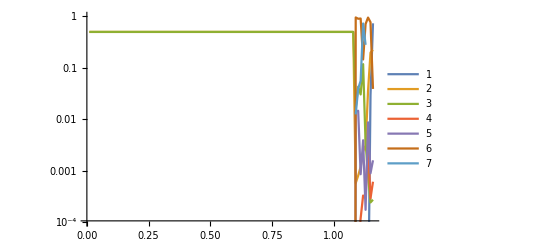

```mathematica
ListLogPlot[{AbundanceMassData[[All,{1,2}]],AbundanceMassData[[All,{1,3}]],AbundanceMassData[[All,{1,4}]],AbundanceMassData[[All,{1,5}]],AbundanceMassData[[All,{1,6}]],AbundanceMassData[[All,{1,7}]],AbundanceMassData[[All,{1,8}]]}, Joined->True,PlotRange->{All,{10^-4,1}},PlotLegends->All]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/lagrangean/abundance.dat",AbundanceMassData,ExportForm->CForm];
```

## Velocity

```mathematica
VelocityData=Import[ParentDirectory[NotebookDirectory[]]<>"/velocity.dat","Table","HeaderLines" -> 3];
```

```mathematica
VelocityMassData=Table[{MassSum[[i]]/Msun,VelocityData[[Time[[1]],i+1]],VelocityData[[Time[[2]],i+1]],VelocityData[[Time[[3]],i+1]],VelocityData[[Time[[4]],i+1]]},{i,1,Length[MassSum]}];
```

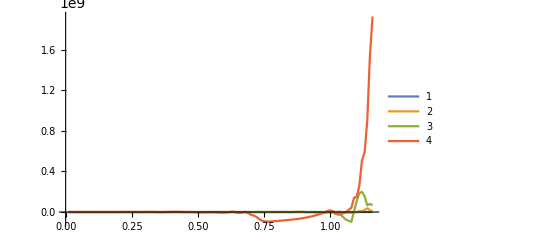

```mathematica
ListPlot[{VelocityMassData[[All,{1,2}]],VelocityMassData[[All,{1,3}]],VelocityMassData[[All,{1,4}]],VelocityMassData[[All,{1,5}]]}, Joined->True,PlotRange->All,PlotLegends->All]
```

```mathematica
Export[ParentDirectory[NotebookDirectory[]]<>"/lagrangean/velocity.dat",VelocityMassData,ExportForm->CForm];
```